```mathematica
f2[z_] =I (z^2-1)/z^2;
g[z_]=z^2(z+1)/(z-1);
f[z_]= f2[z]/g[z];
h[x_] =f[x]/(2){(1-g[x]^2),I  (1+g[x]^2) ,2g[x]} ;
k[z_] = Integrate[h[z1], {z1,1, z}]
sigma[theta_, radius_] =FullSimplify[Re[k[radius Exp[I theta]]],  {radius >10^-10, theta ∈ Reals}];
```

{ConditionalExpression[-(ⅈ (-1+z) (-1+z (2+z (-1+z (7+z (4+z))))))/(6 z^3),Re[z]>0||z∉ℝ],ConditionalExpression[-((-1+z) (1+z) (1+z (-3+z (4+z (3+z)))))/(6 z^3),Re[z]>0||z∉ℝ],ConditionalExpression[ⅈ (-2+1/z+z),Re[z]>0||z∉ℝ]}

-Graphics3D-

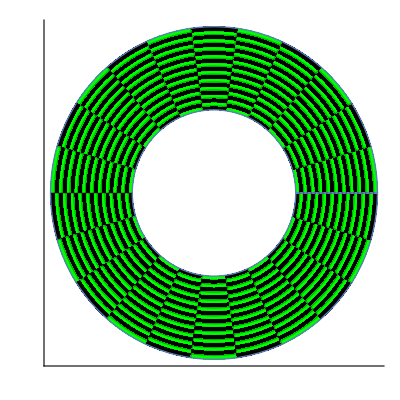

```mathematica
ParametricPlot3D[sigma[theta, rad], {theta,0,2Pi}, {rad,1/2, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{21,20}, PlotTheme->"Minimal"]
ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,0,2Pi}, {rad,1/2, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{21,20}, PlotTheme->"Minimal"]
```

-Graphics3D-

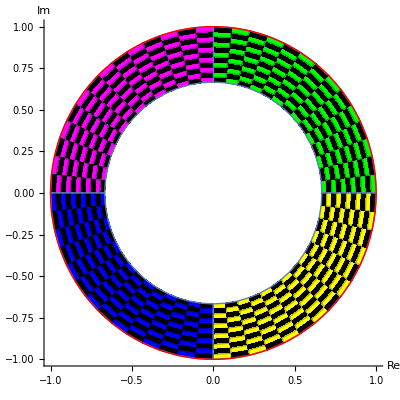

```mathematica
l:= 2/3
mesh1 = 13;
mesh2 = 10;
a = ParametricPlot3D[sigma[theta, rad], {theta,0,Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
b = ParametricPlot3D[sigma[theta, rad], {theta,Pi/2,Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Magenta ,Black},{Black ,Magenta}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
c = ParametricPlot3D[sigma[theta, rad], {theta,Pi,3Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot3D[sigma[theta, rad], {theta,3/2Pi,2Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
f= ParametricPlot3D[sigma[theta, 1], {theta,0,2Pi},PlotRange->All,  MaxRecursion->3,PlotStyle->{Thick, Red}]  ;
Show[a,b,c,d,f]

a = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,0,Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
b = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,Pi/2,Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Magenta ,Black},{Black ,Magenta}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
c = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,Pi,3Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot[{rad Cos [theta], rad Sin[theta]},{theta,3/2Pi,2Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
Show[a,b,c,d, ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π}, PlotStyle->{Thick, Red}], AxesLabel->{Re,Im}, Axes->True, Ticks->{{0,0.5}}]
```

-Graphics3D-

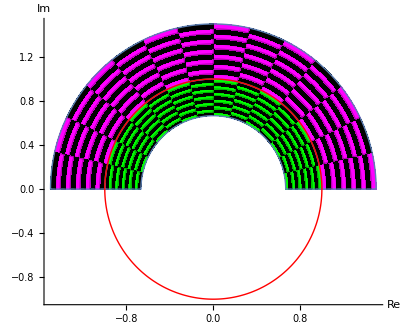

```mathematica
l:= 2/3
mesh1 = 13;
mesh2 = 10;
a = ParametricPlot3D[sigma[theta, rad], {theta,0,Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
b = ParametricPlot3D[sigma[theta, rad], {theta,0,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Magenta ,Black},{Black ,Magenta}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
c = ParametricPlot3D[sigma[theta, rad], {theta,Pi,3Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot3D[sigma[theta, rad], {theta,3/2Pi,2Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
f= ParametricPlot3D[sigma[theta, 1], {theta,0,2Pi},PlotRange->All,  MaxRecursion->3,PlotStyle->{Thick, Red}]  ;
Show[a,b,f]

a = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,0,Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
b = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,0,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Magenta ,Black},{Black ,Magenta}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
c = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,Pi,3Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot[{rad Cos [theta], rad Sin[theta]},{theta,3/2Pi,2Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
Show[a,b, ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π}, PlotStyle->{Thick, Red}], AxesLabel->{Re,Im}, Axes->True, Ticks->{{0,0.5}}]
```

-Graphics3D-

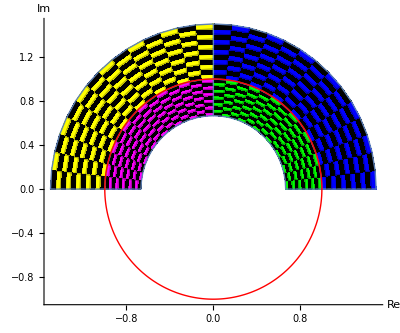

```mathematica
l:= 2/3
mesh1 = 13;
mesh2 = 10;
a = ParametricPlot3D[sigma[theta, rad], {theta,0,Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
b = ParametricPlot3D[sigma[theta, rad], {theta,Pi/2,Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Magenta ,Black},{Black ,Magenta}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
c = ParametricPlot3D[sigma[theta, rad], {theta,0,Pi/2}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot3D[sigma[theta, rad], {theta,1/2Pi,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
f= ParametricPlot3D[sigma[theta, 1], {theta,0,Pi},PlotRange->All,  MaxRecursion->3,PlotStyle->{Thick, Red}]  ;
Show[a,b,c,d,f]

a = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,0,Pi/2}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Green ,Black},{Black ,Green}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
b = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta,Pi/2,Pi}, {rad,l, 1},PlotRange->All,  MaxRecursion->3, MeshShading->{{Magenta ,Black},{Black ,Magenta}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
c = ParametricPlot[{rad Cos [theta], rad Sin[theta]}, {theta, 0,Pi/2}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot[{rad Cos [theta], rad Sin[theta]},{theta,1/2Pi,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
g=ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π}, PlotStyle->{Thick, Red}];
Show[a,b,c,d, g, AxesLabel->{Re,Im}, Axes->True, Ticks->{{0,0.5}}]
```

z

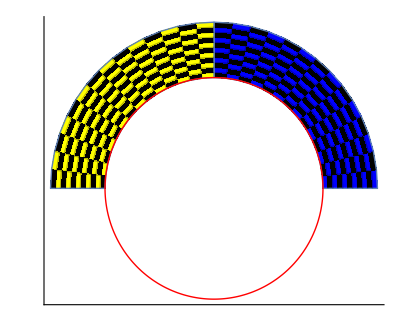

```mathematica
fu[z_] = z
hu[rad_, theta_] = fu[rad Cos [theta]+ I rad Sin[theta]];
c = ParametricPlot[{Re[hu[rad, theta]], Im[hu[rad,theta]]}, {theta, 0,Pi/2}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot[{Re[hu[rad, theta]], Im[hu[rad,theta]]},{theta,1/2Pi,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
Show[c,d, g]
```

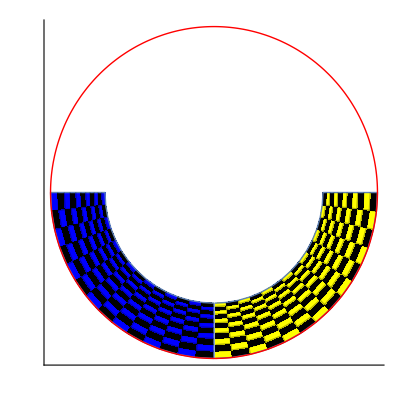

```mathematica
fu[z_] = -1/Conjugate[ z];
hu[rad_, theta_] = fu[rad Cos [theta]+ I rad Sin[theta]];
c = ParametricPlot[{Re[hu[rad, theta]], Im[hu[rad,theta]]}, {theta, 0,Pi/2}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot[{Re[hu[rad, theta]], Im[hu[rad,theta]]},{theta,1/2Pi,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
Show[c,d, g]
```

```mathematica
□_□
```

```mathematica
fu[z_] = -z/Abs[z]^2;
hu[rad_, theta_] = fu[rad Cos [theta]+ I rad Sin[theta]];
c = ParametricPlot[{Re[hu[rad, theta]], Im[hu[rad,theta]]}, {theta, 0,Pi/2}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Blue ,Black},{Black ,Blue}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
d = ParametricPlot[{Re[hu[rad, theta]], Im[hu[rad,theta]]},{theta,1/2Pi,Pi}, {rad,1, 1/l},PlotRange->All,  MaxRecursion->3, MeshShading->{{Yellow ,Black},{Black ,Yellow}},Mesh->{mesh1,mesh2}, PlotTheme->"Minimal"];
Show[c,d, g]
```

-Graphics-